```mathematica
PerBucket=Association[];
Table[PerBucket[allGraphs3[k,"vertexsets"]]={},{k,Keys[allGraphs3]}];
Table[PerBucket[allGraphs3[k,"vertexsets"]]=Append[PerBucket[allGraphs3[k,"vertexsets"]],k],{k,Keys[allGraphs3]}];
Length[PerBucket]
```

5

## Trying to automate base validation

```mathematica
PartitionToSymbol3[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["r"<>end]]
```

```mathematica
BucketLengths=Table[Length[PerBucket[Keys[PerBucket][[k]]]],{k,Length[Keys[PerBucket]]}]
```

{8,2,2,2,1}

```mathematica
NextOption[current_]:=Block[{result=current, l=Length[current],pos, done=False},
pos=l;
While[pos>0 && ! done,
If[result[[pos]]>=BucketLengths[[pos]],
result[[pos]]=1;
pos--,
result[[pos]]=result[[pos]]+1;
done=True
]
];
If[done, result,{}]
]
```

```mathematica
Block[{current=Table[1,{k,Range[Length[BucketLengths]]}],randoms,randomSyms,equations, syms,randomfullsol, rmat, result={}},

syms=Sort[Table[allGraphs3[k,"colofour"],{k,allGraphs3AtomKeys}],CompareSymbols];

Monitor[
While[current≠{},
(* select symbols *)
randoms =Table[PerBucket[Keys[PerBucket][[k]]][[current[[k]]]],{k,Length[Keys[PerBucket]]}];

(* generate symbols *)
randomSyms=Sort[Table[PartitionToSymbol3[allGraphs3[k,"vertexsets"]],{k,randoms}],CompareSymbols];

(* generate equations and solve them *)
equations=Table[PartitionToSymbol3[allGraphs3[k,"vertexsets"]]==allGraphs3[k,"colofour"],{k,randoms}];
randomfullsol=First[Solve[equations,syms]];
rmat=  Map[
Table[Coefficient[#[[2]],t],{t,randomSyms}]&,
randomfullsol];
AppendTo[result,MatrixRank[rmat]];
current=NextOption[current]
],
current];
result
]
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

## Old stuff

```mathematica
Product[m,{m,Table[Length[PerBucket[k]],{k,Keys[PerBucket]}]}]
```

64

```mathematica
Table[Log[2,Length[PerBucket[k]]],{k,Keys[PerBucket]}]//Tally//Sort
```

{{0,1},{1,3},{3,1}}

```mathematica
randoms =Sort[Table[First[RandomSample[PerBucket[k],1]],{k,Keys[PerBucket]}],CompareSymbols[SetsToSymbol2[allGraphs3[#1,"vertexsets"]],SetsToSymbol2[allGraphs3[#2,"vertexsets"]]]&]
```

{3,14,18,6,26}

```mathematica
Table[Labeled[allGraphs3[k,"graph"],Style[k,ColourForKey[allGraphs3,k]]],{k,randoms}]
```

{-Graphics-3,-Graphics-14,-Graphics-18,-Graphics-6,-Graphics-26}

```mathematica
randomSyms=Sort[Table[PartitionToSymbol3[allGraphs3[k,"vertexsets"]],{k,randoms}],CompareSymbols]
```

{r1x2x3,r1x23,r12x3,r13x2,r123}

```mathematica
syms=Sort[Table[allGraphs3[k,"colofour"],{k,allGraphs3AtomKeys}],CompareSymbols]
```

{v1x2x3,v1x23,v12x3,v13x2,v123}

```mathematica
randomRep2=Table[PartitionToSymbol3[allGraphs3[k,"vertexsets"]]->Tooltip[Labeled[allGraphs3[k,"graph"],Style[k,ColourForKey[allGraphs3,k]]],allGraphs3[k,"compwhy"]],{k,randoms}];
```

```mathematica
randommat=Table[PartitionToSymbol3[allGraphs3[k,"vertexsets"]]==allGraphs3[k,"colofour"],{k,randoms}];TableForm[randommat];
```

```mathematica
randomfullsol=First[Solve[randommat,syms]]
```

{v1x2x3→r123-r12x3-r1x23+r1x2x3,v1x23→r1x23,v12x3→-r123+r12x3,v13x2→-r123+r13x2,v123→r123}

```mathematica
TableForm[
Table[
Labeled[allGraphs3[k,"graph"],Style[k,ColourForKey[allGraphs3,k]]]->
{allGraphs3[k,"colofour"]/.randomfullsol/.randomRep2,allGraphs3[k,"colofour"]/.randomfullsol},
{k,allGraphs3AtomKeys}
]
]
```

-Graphics-13→{-Graphics-26--Graphics-18--Graphics-14+-Graphics-3,r123-r12x3-r1x23+r1x2x3}
-Graphics-14→{-Graphics-14,r1x23}
-Graphics-16→{--Graphics-26+-Graphics-6,-r123+r13x2}
-Graphics-22→{--Graphics-26+-Graphics-18,-r123+r12x3}
-Graphics-26→{-Graphics-26,r123}

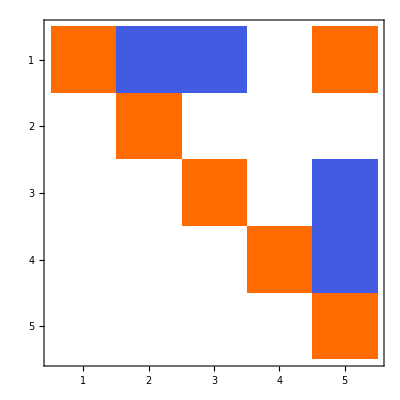

```mathematica
rmat=  Map[
Table[Coefficient[#[[2]],t],{t,randomSyms}]&,
randomfullsol];MatrixPlot[rmat]
```

```mathematica
MatrixRank[rmat]
```

5

```mathematica
32
```

32

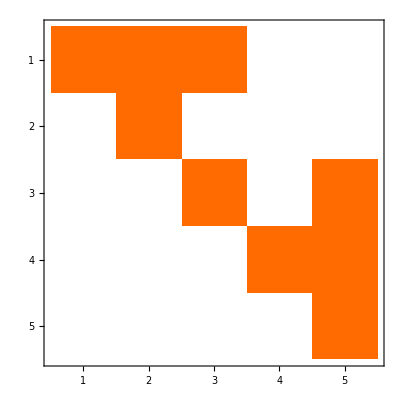

```mathematica
Inverse[rmat]//MatrixPlot
```